## Ex. 1 - 1D Single- and N-Slit

#### Single Slit

```mathematica
A2[x2_,z_]:= ((-ⅈ k)/(2 π z))^(1/2)ⅇ^(ⅈ k/(2 z)x2^2)∫_(-a/2)^(a/2) A1[x1] ⅇ^(-ⅈ k/(2 z)x1 x2)ⅆx1;
```

Let the front focal plane field A1 be apertured by a slit of width 10 um:

```mathematica
k = 2π/7.8*^-9; f= .1; a = 1*^-5;
```

```mathematica
A1[x_]:=1; (*the integral is only evaluated where the field is nonzero; no need for peicewise definition*)
```

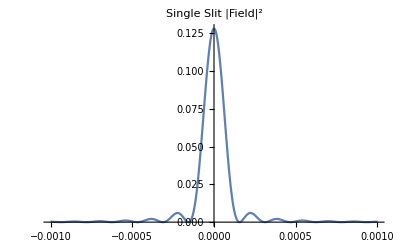

```mathematica
Plot[Evaluate[A2[x, f]*A2[x,f]], {x, -1*^-3,1*^-3}, PlotRange->Full, PlotLabel->"Single Slit |Field|^2"]
```

Analytically,

```mathematica
Clear[k,a]
```

```mathematica
∫_(-a/2)^(a/2) 1*ⅇ^(-ⅈ k/(2 z)x1 x2)ⅆx1
```

(4 z Sin[(a k x2)/(4 z)])/(k x2)

This is 1/a Sinc[a k x2/(4 z)]

#### N Slits

Define the input field being apetured by multiple slits d center to center

```mathematica
d = 3a;
comb[x_]= Sum[DiracDelta[x-j d],{j, }]... TBD
```

## Circular Apertures

For the field in the back focal plane of a lens f, illuminated from the front focal plane by a plane wave apertured by a hole of radius a, (and setting k_perp = ρ1k/f = 1), we have:

```mathematica
∫_0^a 2π BesselJ[0,ρ0]ⅆρ0
```

a π (π BesselJ[1,a] StruveH[0,a]+BesselJ[0,a] (2-π StruveH[1,a]))

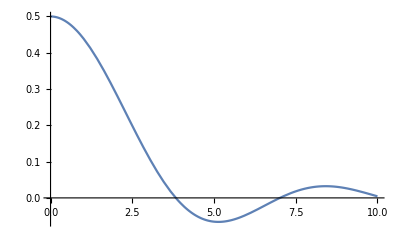

```mathematica
Plot[BesselJ[1,x]/x, {x, 0, 10}]
```

## N Slit Interference

A single rectangular slit has interference pattern Sinc[(k a x)/(2L)]. With N slits, this is modulated by Sin[(N k h x)/(2 L)]/Sin[(k h x)/(2 L)] where h is the distance between slits.

```mathematica
n = 10; k = 2π/1.064*^-6; a = 1*^-5; h = 3 a; L = .1;
```

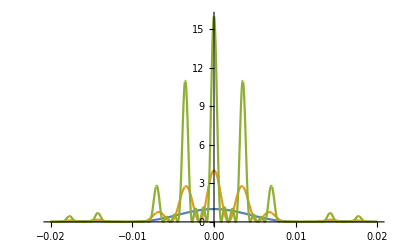

```mathematica
Plot[Evaluate[Table[Sinc[(k a x)/(2 L)]^2(Sin[(n k h x)/(2 L)]/Sin[(k h x)/(2 L)])^2,{n,{1,2,4}}]], {x, -.02,.02}, PlotRange->Full]
```

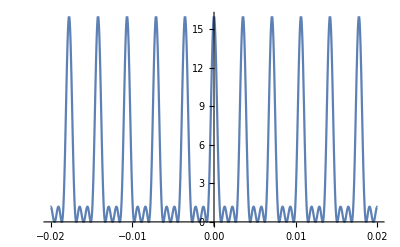

```mathematica
Plot[(Sin[(4 k h x)/(2 L)]/Sin[(k h x)/(2 L)])^2, {x, -.02,.02}]
```

```mathematica
FourierTransform[Sin[2π k x]/Sin[2π k/4],x,k] (*k-> kh/πL*)
```

```mathematica
Clear[k]
```

## Periodic Array Of Circular Apertures

Output field from 4f config (see Mark array generator proposal)

```mathematica
(*params*)
```

Can add some assumptions below?

```mathematica
Integrate[(Sin[nx (k dx)/(2 f1)x1]Sin[ny (k dy)/(2 f1)y1])/(Sin[(k dx)/(2 f1)x1]Sin[(k dy)/(2 f1)y1])BesselJ[1,a k/f1 √(x1^2+y1^2)]/(√(x1^2+y1^2))Exp[-ⅈ/(2 f2)(x1^2+y1^2)((z2/f2-1)+2(x1 x2 + y1 y2))],{x1,-b,b},{y1, -√(b^2-x1^2),√(b^2-x1)}]
```

∫_-b^b ∫_(-√(b^2-x1^2))^(√(b^2-x1)) 1/(√(x1^2+y1^2))ⅇ^(-(ⅈ (x1^2+y1^2) (f2 (-1+2 x1 x2+2 y1 y2)+z2))/(2 f2^2)) BesselJ[1,(a k √(x1^2+y1^2))/f1] Csc[(dx k x1)/(2 f1)] Csc[(dy k y1)/(2 f1)] Sin[(dx k nx x1)/(2 f1)] Sin[(dy k ny y1)/(2 f1)]ⅆy1ⅆx1